{{2.,2.5},{-2.5,2.},{-0.5,3.5},{3.,1.},{3.,-0.5}}

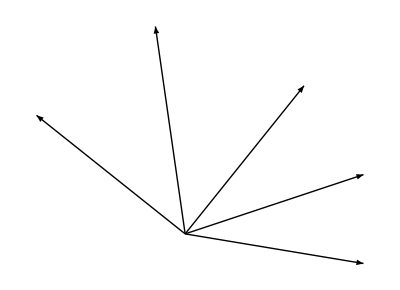

{0.896055,2.46685,1.71269,0.321751,0.165149}

```mathematica
points={{1.5,1.5},{3.5,4},{-1,3.5},{1,5},{4.5,2.5},{4.5,1}};
arrows=
Drop[
Map[
#1 - points[[1]]&,
points],
1]
Graphics[Map[Arrow[{points[[1]],#1}]&,Drop[points,1]]]
angles=
Map[
VectorAngle[#1,{1,0}]&,
arrows]
```